# Flammability limits

This notebook is designed to reproduce the 3 flammability limits that are observed when burning a hydrogen-air mixture. The code is not well-designed, but it seems to work, if you can do better, feel free to improve it.

The values of constants and kinetic equations are taken from the author of the KINET program A . V . Abramenkov (Lomonosov MSU, Moscow) .

## Extract data from file

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
str=StringDelete[RegularExpression["#.*"]]@Import["data/H2Burn.kin","Text"];
```

```mathematica
lines=Replace[
StringSplit[StringSplit[str,"\n"],RegularExpression[",\\s+"]],
{{eq_,k_}:>{eq,k,0,0},{eq_,A_,Ea_}:>{eq,A,Ea,0}},
1
];
```

```mathematica
{reactionStrings,preExponential,activations,empirical}=Transpose@lines;
```

```mathematica
preExponential=Interpreter["Number"]@*StringDelete[RegularExpression["\\s+"]]/@StringTrim[preExponential,{"k = "}]/.Null->0;
```

```mathematica
activations=1000ToExpression/@activations/.Null->0;
```

```mathematica
empirical=ToExpression/@empirical;
```

```mathematica
rules=Rule@@@(StringSplit[#," + "]&/@StringSplit[reactionStrings," = "])/.Null->0;
```

```mathematica
reagents=DeleteDuplicates@Flatten[List@@@rules];
```

## Transform data to system of equations

```mathematica
makeEq[reag_]:=Module[{mask,factors,act,pre,emp,consts},
mask=Map[Not@*FreeQ[reag],rules];
factors=Cases[Pick[rules,mask],HoldPattern[r_->p_]:>Times@@(c[#][t]&/@r)(Count[reag]@p-Count[reag]@r)];
act=Pick[activations,mask];
pre=Pick[preExponential,mask];
emp=Pick[empirical,mask];
consts=Replace[Transpose[{pre,act,emp}],{a_,e_,n_}:>a (T/298)^n Exp[-e/(8.31 T)],1];
c[reag]'[t]==factors.consts
]
```

```mathematica
makeSys[init_,temp_]:=Module[{eqs,inits,unconditioned,sys},
eqs=makeEq/@reagents;
unconditioned=Complement[reagents,First/@init];
inits=init/.HoldPattern[r_->conc_]:>c[r][0]==conc;
unconditioned=c[#][0]==0&/@unconditioned;

sys=Join[eqs,inits,unconditioned]/.T->temp;

(* Remove equations with implicit particles *)
sys=Select[sys,FreeQ[#,c["M"]'[t]==0.]&&FreeQ[#,c["M"][0]]&];

(* Write down the material balance explicitly *)
sys=sys/.c["M"][t]->c["H2"][t]+c["N2"][t]+c["O2"][t];

(* Replace the nitrogen with the total concentration *)
sys=sys/.c["N2"][_]->cN2;

(* Remove trivia *)
sys=sys/.True->Nothing;

sys
]
```

```mathematica
vars=DeleteDuplicates@DeleteCases[Map[c[#][t]&,reagents],c["M"][t]];
```

```mathematica
sol[cH2_, cO2_, cN2_, T_, tmax_] :=
	Quiet@Module[{end = 1, sol1},
		sol1 = First @ NDSolve[
			makeSys[{"H2" -> cH2, "O2" -> cO2, "N2" -> cN2}, T],
			vars,
			{t, 0, tmax},
			Method -> {
				"EventLocator",
				"Event" -> {c["H2"][t] ≤ cH2 / 2 || c["O2"][t] ≤ cO2 / 2},
				"EventAction" :> Throw[end = t, "StopIntegration"]
			}
		];
		{sol1, end}
	]
```

## Define measurable metrics

```mathematica
ClearAll[duration];
duration[p_,T_]:=Module[{
coeffs={6.9797,1.4657,5.5140}10^-3,
press
},
press=coeffs{p,p,p};
Last@sol[Sequence@@press,T,1]
]
```

```mathematica
ClearAll[calculate];
calculate[{logPmin_, logPmax_}, {Tmin_, Tmax_}, grid_:10] :=
	Flatten[#, 1]& @ ParallelTable[
		{T, p, -Log10 @ duration[p, T]},
		{p, 10^Subdivide[logPmin, logPmax, grid]},
		{T, Subdivide[Tmin, Tmax, grid]}
	];
```

## Start parallel calculations and plot results

```mathematica
data=calculate[{-3,3},{600,1000},10];
```

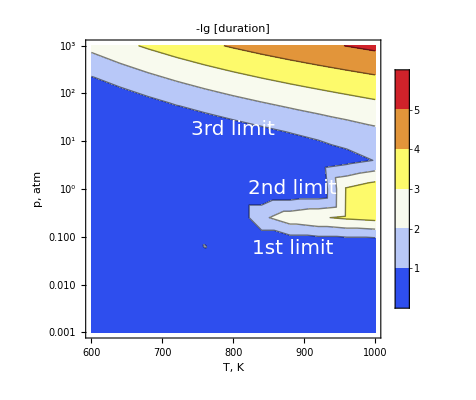

```mathematica
ListContourPlot[
data,
ClippingStyle->Automatic,
ScalingFunctions->{None,"Log10"},
Epilog->{
Text[Style["1st limit",20,White],Scaled[{.7,.3}]],
Text[Style["2nd limit",20,White],Scaled[{.7,.5}],Automatic,{1,0.4}],
Text[Style["3rd limit",20,White],Scaled[{.5,.7}],Automatic,{1,-0.2}]
},
FrameLabel->{"T, K","p, atm"},
PlotLegends->Automatic,
ColorFunction->"TemperatureMap",
PlotLabel->"-lg [duration]"
]
```